# Fractal Substitution by L-system (the Hat tile)

## Begin With Edges

Here we only care about edges, even boundary. Maybe later we will consider something about vertex replacement.

This is to generate corresponding really edges, for visualization.

```mathematica
edgeProduce={
e[1|2|5|6|9|10][dir_]:>Sqrt[3]ReIm[Exp[dir*Pi/6 I]],
e[3|4|7|8|11|12|13|14][dir_]:>ReIm[Exp[dir*Pi/6 I]]
};
```

### Replace Rules

Replace a sequence of edges. Obtained by observing factual substitution process.

```mathematica
edgeReplaceRule=
{
{
e[6][dir_],e[7][_],e[8][_],e[9][_],e[10][_],e[11][_]
}:>{
e[4][dir+5],e[5][dir+2],
e[6][dir],e[7][dir+3],e[8][dir+1],e[9][dir+4],e[10][dir+2],e[11][dir+5],
e[12][dir+3],e[13][dir+3],e[14][dir+5],e[1][dir+2]
},
{
e[2][dir_],e[3][_]
}:>{
e[4][dir+5],e[5][dir+2],
e[2][dir],e[3][dir+3],
e[12][dir+1],e[13][dir+1],e[14][dir+3],e[1][dir]
},

{
e[12][dir_],e[13][_],e[14][_],e[1][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2],
e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1],
e[2][dir+1],e[3][dir+4]
},
{
e[4][dir_],e[5][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2]
}
};
```

### Basic Edges

We need some information for one single hat tile. It starts with edge 2, it’s for the convenience of sequence replacing.

```mathematica
basicEdges[dir_:0]:={
e[2][dir+1],e[3][dir+4],
e[4][dir+6],e[5][dir+3],
e[6][dir+5],e[7][dir+8],e[8][dir+6],e[9][dir+9],e[10][dir+7],e[11][dir+10],
e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1]
};
```

Pack a function to simplify nest code later.

```mathematica
substitute["e"][edgeList_List]:=Catenate[SequenceReplace[edgeList,edgeReplaceRule]];
```

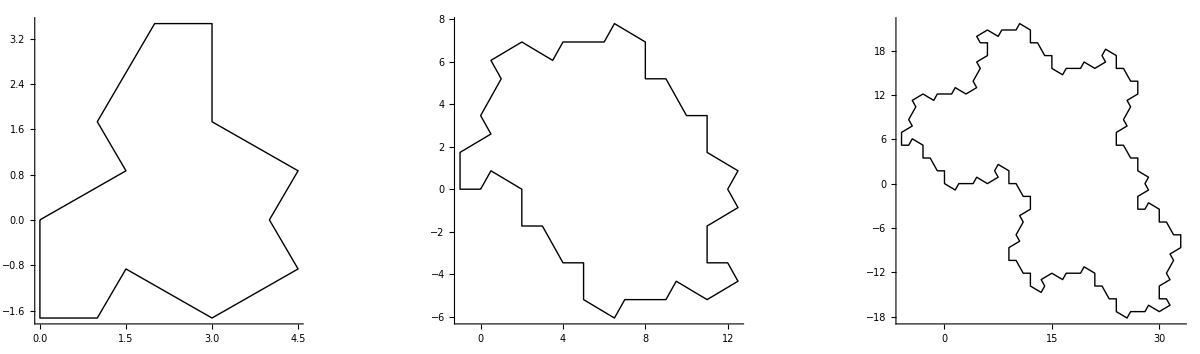

```mathematica
GraphicsRow[
Riffle[
Graphics[Line[#],Axes->True]&/@{
FoldList[Plus,{0,0},basicEdges[8]/.edgeProduce],
FoldList[Plus,{0,0},substitute["e"][basicEdges[8]]/.edgeProduce],
FoldList[Plus,{0,0},Nest[substitute["e"],basicEdges[8],2]/.edgeProduce]
},
Style["→",50,Purple]
]
]
```

It is hard to split list and replace and join every time. Let’s do more analysis:

## Treat Sequence of Edges as a Whole

```mathematica
{Column[#1],Style["→",40],Column[#2]}&@@@edgeReplaceRule//Grid[#,Frame->{False,All},FrameStyle->LightGray,Spacings->{3,5}]&
```

Notice that there is not any overlap in terms of edge index on the left-hand side, which means we have a partition of edges as:

```mathematica
{
{e[6],e[7],e[8],e[9],e[10],e[11]},
{e[2],e[3]},
{e[12],e[13],e[14],e[1]},
{e[4],e[5]}
}
```

{{e[6],e[7],e[8],e[9],e[10],e[11]},{e[2],e[3]},{e[12],e[13],e[14],e[1]},{e[4],e[5]}}

Each group always shows up together and in order, no matter on the left hand side or right hand side.

So, there are only four important equivalent edges, let’s name them:

```mathematica
EToEdges={
E[1][dir_]:>Sequence@@{e[6][dir],e[7][dir+3],e[8][dir+1],e[9][dir+4],e[10][dir+2],e[11][dir+5]},
E[2][dir_]:>Sequence@@{e[2][dir],e[3][dir+3]},
E[3][dir_]:>Sequence@@{e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1]},
E[4][dir_]:>Sequence@@{e[4][dir],e[5][dir-3]}
};
```

Use E to represent replaceRule:

```mathematica
EReplaceRule={
E[1][dir_]:>{E[4][dir+5],E[1][dir],E[3][dir+3]},
E[2][dir_]:>{E[4][dir+5],E[2][dir],E[3][dir+1]},
E[3][dir_]:>{E[2][dir-3],E[3][dir-2],E[2][dir-1],E[3][dir],E[2][dir+1]},
E[4][dir_]:>{E[2][dir-3],E[3][dir-2],E[2][dir-1]}
};
```

These rules are much simpler. And pack a function for convenience:

```mathematica
substitute["E"][EList_List]:=Join@@ReplaceAll[EList,EReplaceRule];
```

basicE corresponds to basicEdges.

```mathematica
basicE[dir_]:={E[2][dir+1],E[4][dir+6],E[1][dir+5],E[3][dir+0]};
```

### Build Full Tiling

```mathematica
completeTile=Append[
Switch[First[Head[#]],
1,RotateLeft[basicE[First[#]-5],2],
2,RotateLeft[basicE[First[#]-1],0],
3,RotateLeft[basicE[First[#]],-1],
4,RotateLeft[basicE[First[#]-6],1]
],#]&;
```

```mathematica
buildTiling[or_:{0,0},dir_:0,level_:0]:=FoldList[Plus,or,
Nest[
Catenate[completeTile/@substitute["E"][#]]&,
basicE[dir],level
]/.EToEdges/.edgeProduce]
```

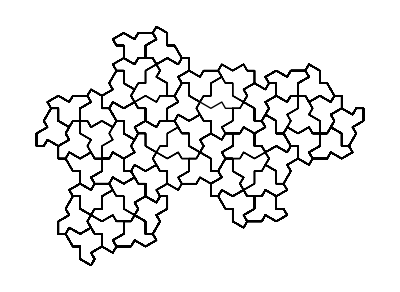

```mathematica
Line[buildTiling[{0,0},10,2]]//Graphics
```

### Build Tile Boundary

```mathematica
buildTileBoundary[or_:{0,0},dir_:0,level_:0]:=FoldList[Plus,or,Nest[substitute["E"],basicE[dir],level]/.EToEdges/.edgeProduce]
```

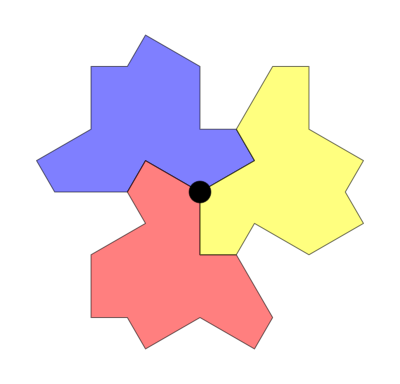
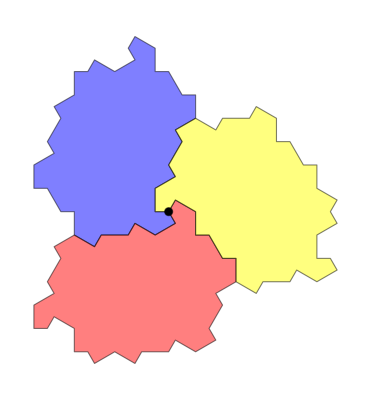
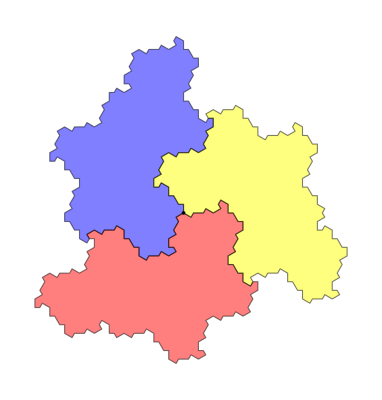

```mathematica
With[{scalar=0},
Graphics[
{
EdgeForm[Black],Opacity[.5],
Blue,Polygon@buildTileBoundary[-scalar ReIm[Exp[Pi/3I]],0,#]
,Red,Polygon@buildTileBoundary[-scalar ReIm[Exp[9Pi/3I]],4,#]
,Yellow,Polygon@buildTileBoundary[-scalar ReIm[Exp[5Pi/3I]],8,#]
,Black,Opacity[1],Disk[{0,0},.3]
}
]
]&/@Range[0,2]
```

## Add Reflected Substitution

### Full rules

```mathematica
edgeReplaceRule=
{
(*counter clock-wise*)
{e[6][dir_],e[7][_],e[8][_],e[9][_],e[10][_],e[11][_]}:>{
e[4][dir+5],e[5][dir+2],
e[6][dir],e[7][dir+3],e[8][dir+1],e[9][dir+4],e[10][dir+2],e[11][dir+5],
e[12][dir+3],e[13][dir+3],e[14][dir+5],e[1][dir+2]
},
{
e[2][dir_],e[3][_]
}:>{
e[4][dir+5],e[5][dir+2],
e[2][dir],e[3][dir+3],
e[12][dir+1],e[13][dir+1],e[14][dir+3],e[1][dir]
},

{
e[12][dir_],e[13][_],e[14][_],e[1][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2],
e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1],
e[2][dir+1],e[3][dir+4]
},
{
e[4][dir_],e[5][_]
}:>{
e[2][dir-3],e[3][dir],
e[12][dir-2],e[13][dir-2],e[14][dir],e[1][dir-3],
e[2][dir-1],e[3][dir+2]
}
(*clock-wise*)
,
{e[11][_],e[10][_],e[9][_],e[8][_],e[7][_],e[6][dir_]}:>{
e[1][2+dir],e[14][5+dir],e[13][3+dir],e[12][3+dir],
e[11][5+dir],e[10][2+dir],e[9][4+dir],e[8][1+dir],e[7][3+dir],e[6][dir],
e[5][2+dir],e[4][5+dir]
},
{e[3][_],e[2][dir_]}:>{
e[1][dir],e[14][3+dir],e[13][1+dir],e[12][1+dir],
e[3][3+dir],e[2][dir],
e[5][2+dir],e[4][5+dir]
},
{e[1][_],e[14][_],e[13][_],e[12][dir_]}:>{
e[3][4+dir],e[2][1+dir],
e[1][-1+dir],e[14][2+dir],e[13][dir],e[12][dir],
e[3][2+dir],e[2][-1+dir],
e[1][-3+dir],e[14][dir],e[13][-2+dir],e[12][-2+dir],
e[3][dir],e[2][-3+dir]
},
{e[5][_],e[4][dir_]}:>{
e[3][2+dir],e[2][-1+dir],
e[1][-3+dir],e[14][dir],e[13][-2+dir],e[12][-2+dir],
e[3][dir],e[2][-3+dir]
}
};
```

### Example

```mathematica
H7Boundary={
e[12][8],e[13][8],e[14][10],e[1][7],
e[2][-3],e[3][0],
e[12][-2],e[13][-2],e[14][0],e[1][-3],
e[2][-1],e[3][2],
e[12][0],e[13][0],e[14][2],e[1][-1],
e[2][1],e[3][4],
e[4][6],e[5][3],
e[2][1],e[3][4],
e[12][2],e[13][2],e[14][4],e[1][1],
e[2][3],e[3][6],
e[12][4],e[13][4],e[14][6],e[1][3],
e[2][5],e[3][8],
e[4][10],e[5][7],

e[5][9],e[4][0],
e[3][-2],e[2][7],
e[1][5],e[14][8],e[13][6],e[12][6]
};
```

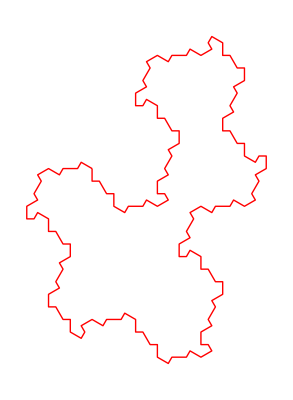

```mathematica
With[{edgeSequence=Nest[Catenate[SequenceReplace[#,edgeReplaceRule]]&,H7Boundary,1]},
Graphics[{Thick,Red,Line[FoldList[Plus,{0,0},edgeSequence/.edgeProduce]]}]
]
```